## RQ decomposition

I want to do a QR backwards for practice.  I am going to rewrite the code from 4610/5627 and incorporate the Q build.

### Matrix Version

```mathematica
MyRQMatrixFull[A_]:= Module[{R=A,Q,H,m,n,v},
(* Assumme is m≤n *)
{m,n}=Dimensions[R];
Q=IdentityMatrix[n];
Do[
v=R⟦m-i,All⟧; v⟦n+1-i;;n⟧*=0;v⟦n-i⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q,
{i,0,Min[m-1,n]}];
{Chop[R],Q}
]
```

Testing

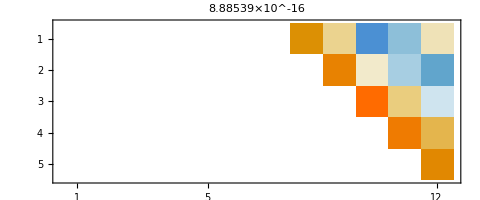

```mathematica
{m,n}={5,12};
A=RandomReal[{-1,1},{m,n}];
{R,Q}=MyRQMatrixFull[A];
MatrixPlot[R,PlotLabel->Norm[A-R.Q]]
```

```mathematica
MatrixPlot[R,PlotLabel->Norm[A-R.Q]]
```

### Action Version

# Break

```mathematica
MatrixPlot[Q]
```

```mathematica
MatrixPlot[R,PlotLabel->Map[Norm,{A-R.Q⟦-m;;-1⟧}]]
```

```mathematica
MatrixPlot[R,PlotLabel->Map[Norm,{A-R.Q}]]
```

To do it the other way around I need to first make sure I understand how to zero the bottom row of of a short fat matrix with a householder

```mathematica
R=A;Q=IdentityMatrix[n];

v=R⟦m,All⟧; v⟦n⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-1,All⟧; v⟦n-0;;n⟧*=0;v⟦-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-2,All⟧; v⟦n-1;;n⟧*=0;v⟦n-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]

v=R⟦m-3,All⟧; v⟦n-2;;n⟧*=0;v⟦n-3⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]
```

```mathematica
{m,n}={12,12};
A=RandomReal[{-1,1},{m,n}];
{Q2,R2}=MyQR[A];
MatrixPlot[R2]
Norm[A-Q2.R2]
```

```mathematica
R=A;Q=IdentityMatrix[n];

TabView[
Table[
v=R⟦m-i,All⟧; v⟦n+1-i;;n⟧*=0;v⟦n-i⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q;
Map[MatrixPlot,Chop[{R,Q}]],
{i,0,Min[m-1,n]}]
]
```

```mathematica
Map[MatrixPlot,{R1,R2}]
```

```mathematica
Norm[Qᵀ.Q-IdentityMatrix[n]]
MatrixPlot[Chop[A.Qᵀ],
PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-R.Q}]]
```

```mathematica
v=R⟦m,All⟧; v⟦n⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=H.Q;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-1,All⟧; v⟦n-0;;n⟧*=0;v⟦-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H,Qᵀ.Q}]]

v=R⟦m-2,All⟧; v⟦n-1;;n⟧*=0;v⟦n-2⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]

v=R⟦m-3,All⟧; v⟦n-2;;n⟧*=0;v⟦n-3⟧-=Norm[v]; v=v/Norm[v];
H=IdentityMatrix[n]-2 KroneckerProduct[v,v];
R=R.H; Q=Q.H;
Map[MatrixPlot,Chop[{A.Q,R,H, Qᵀ.Q}]]
```

```mathematica
MyRQ[AIn_]:= Module[{A=AIn,m,n,v,V},
{m,n}=Dimensions[A];
V=ConstantArray[0,{m,n}];
(* Householder Reduction from Script Version 3 *)
Do[
v=A⟦1;;i,i⟧;
v⟦-11⟧-=Norm[v]; v=v/Norm[v];
V⟦i;;1,i⟧=v;
Do[
A⟦1;;i,j⟧=A⟦1;;i,j⟧-2 v (v.A⟦1;;i,j⟧),
{j,i,n}],
{i,n,2,-1}];
(* Returns Householder vectors in V *)
{Chop[A],V}
]
```

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{R1,V1}=MyQR[A];
{R2,V2}=MyRQ[A];
Map[SingularValueList,{A,R}]
MatrixPlot[R]
```

```mathematica
QRDecomposition[A_]:=
```

```mathematica
RQDecomposition[A_]:= Module[{Q,R=A},
```

I am

```mathematica
$VersionNumber
```

```mathematica
QRDecomposition
```

# Implicit Q consequences.

I want to run an implict bulge chase simultaneously from the top and the bottom.  I need to use a “consistent +” Hessenberg to understand this.  I think a “consistent  +“ diagonal QR might also be useful.  Again this is essentially for uniqueness.

Below is edited (adding V store and reverse Q construction) from CLass.  Needed for +def sign convention which ius required for uniqueness!

```mathematica
QRPlus[A_]:= Module[{R=A,Q, m,n,x,v,V},
(* Compute R and store vs in V *)
{m,n}=Dimensions[A];
V=V=ConstantArray[0,{m,m}];
(* Build R *)
Do[
x=R⟦k;;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧-Norm[v];(* positive on subdiagonal choice *)
v=Normalize[v];
V⟦k;;m,k⟧=v;
R⟦k;;m,k;;n⟧=R⟦k;;m,k;;n⟧-2 KroneckerProduct[v,v.R⟦k;;m,k;;n⟧],
{k,1,n}];
(* Build Q *)
Q=Normal[SparseArray[Band[{1,1}]->1.0,{m,n}]];
Do[
v=V⟦k;;m,k⟧;
Q⟦k;;m,1;;n⟧=Q⟦k;;m,1;;n⟧-2 KroneckerProduct[v,v.Q⟦k;;m,1;;n⟧],
{k,n,1,-1}];
(* return stuff *)
{Q,R⟦1;;n,1;;n⟧}]
```

```mathematica
{m,n}={123,8};
A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRPlus[A];
MatrixPlot[Chop[R], PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R}]]
```

Below is edited (adding V store and reverse Q construction) from Class.  Needed for +def sign convention which is required for uniqueness!

```mathematica
HessenbergReductionPlus[AIn_]:= Module[{A=AIn, m=Length[AIn],v,x, Q,V},
V=ConstantArray[0,{m,m}];
(* Compute H and store vs in V *)
Do[
x=A⟦(k+1);;m,k⟧;
v=x; v⟦1⟧=v⟦1⟧-Norm[x];(* positive on subdiagonal choice *)
v=Normalize[v];
V⟦(k+1);;m,k⟧=v;
A⟦(k+1);;m,k;;m⟧=A⟦k+1;;m,k;;m⟧-2 KroneckerProduct[v,v.A⟦(k+1);;m,k;;m⟧];
A⟦1;;m,(k+1);;m⟧=A⟦1;;m,(k+1);;m⟧-2 KroneckerProduct[A⟦1;;m,(k+1);;m⟧.v,v],
{k,1,m-1}];
(* Compute and Store Q *)
Q=IdentityMatrix[m];
Do[
v=V⟦(k+1);;m,k⟧;
Q⟦(k+1);;m,1;;m⟧=Q⟦k+1;;m,1;;m⟧-2 KroneckerProduct[v,v.Q⟦(k+1);;m,1;;m⟧],
{k,m-1,1,-1}];
(* Return things *)
{Q,Chop[A]}]
```

```mathematica
m=12;
A1=RandomReal[{-1,1},{m,m}];
{Q1,H1}=HessenbergReductionPlus[A1];
SubDiagonal1=Diagonal[H1,-1];
J=Reverse[IdentityMatrix[m]]; 
A2=A1.J;
{Q2,H2}=HessenbergReductionPlus[A2];
SubDiagonal2=Diagonal[H2,-1];
GraphicsGrid[{{MatrixPlot[H1,PlotLabel->Map[Norm,{Min[H1],Q1ᵀ.Q1-IdentityMatrix[m],H1-Q1ᵀ.A1.Q1}]],MatrixPlot[H2,PlotLabel->Map[Norm,{Min[H2],Q2ᵀ.Q2-IdentityMatrix[m],H2-Q2ᵀ.A2.Q2}]]}}]
```

```mathematica
m=12;
J=Reverse[IdentityMatrix[m]];
A1=RandomReal[{-1,1},{m,m}];
A2=Reverse[A1]ᵀ;
{Q1,H1}=HessenbergDecomposition[A1];
{Q2,H2}=HessenbergDecomposition[A2];
Map[MatrixPlot,{Q1,Q2,Q1.Q2}]
Map[MatrixPlot,{H1,H2}];
```

```mathematica
m=4;
J=Reverse[IdentityMatrix[m]];
R=UpperTriangularize[Array[r,{m,m}]];
A=Array[a,{m,m}];
TabView[
Map[MatrixForm,{A,J.J,J.A,A.J}]
];
TabView[
Map[MatrixForm,{R,J.R.J}]]
```

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}];
Id=IdentityMatrix[m];
H=HessenbergDecomposition[A]⟦2⟧;
{μ1,μ2}={1,2};
MatrixPlot[(H-μ1 Id).(H-μ2 Id)]
```